## Static Quadrupole Moment

### Calculation of the SQM of wobbling states in odd-mass nuclei The SQM is determined from the diagonal elements of the quadrupole transition operator ℳ(E2), meaning that I|ℳ(E2)|I

### The static quadrupole moment can be determined from the transition quadrupole moment Q_I , which is given by the off-diagonal matrix elements: ⟨I||ℳ(E2)||I-2⟩ for intraband transitions {initial: I→ final: I-2} Q_I=√(16/(5π))B(E2;I->I-2)×C_(K 0 K)^(I 2 I-2) Q_SQM(I)=C_(K 0 K)^(I 2 I)C_(I 0 I)^(I 2 I)×Q_I

## Theoretical Q_I

#### From the theoretical transition quadrupole moment calculate the SQM via the formula containing the two Clebsch-Gordan coefficients

```mathematica
ClearAll["Global`*"]
```

```mathematica
QLu161167TSD1={8.89,8.91,8.92,8.94,8.95,8.96,8.97,8.98};
QLu161167TSD2={8.92,8.93,8.95,8.96,8.97,8.98,8.98};
QLu163TSD1={8.89,8.77,8.66,8.57,8.50,8.43,8.36,8.31};
QLu163TSD2={8.71,8.62,8.53,8.46,8.39,8.34,8.28};
QLu163TSD1Exp={9.93,9.34,8.32,8.93,8.37,7.45,7.37,7.63};
QLu163TSD2Exp={8.51,8.67,8.88,7.82,7.91,6.66,6.68};
QLu165TSD1={10.12,10.14,10.16,10.18,10.19,10.21,10.22,10.23};
QLu165TSD2={10.15,10.17,10.19,10.20,10.21,10.22,10.23};
```

```mathematica
cIK[I_,K_]:=ClebschGordan[{I,K},{2,0},{I,K}];
cII[I_]:=ClebschGordan[{I,I},{2,0},{I,I}];
K0=1/2;
K1=13/2;
```

```mathematica
spinsTSD1=Table[i/2,{i,41,69,4}];
spinsTSD2=Table[i/2,{i,47,71,4}];
```

```mathematica
SQM[Q_,I_,K_]:=SetPrecision[cIK[I,K]*cII[I]*Q,3];
SQMValuesKfixed[qvalues_,spins_,K_]:=Table[SQM[qvalues[[i]],spins[[i]],K],{i,1,Length[qvalues]}];
SQMValues[qvalues_,spins_]:=Table[SQM[qvalues[[i]],spins[[i]],spins[[i]]],{i,1,Length[qvalues]}];
```

### Numerical results

```mathematica
SQMValuesKfixed[QLu161167TSD1,spinsTSD1,K0]
SQMValuesKfixed[QLu161167TSD2,spinsTSD1,K0]
SQMValuesKfixed[QLu163TSD1,spinsTSD1,K0]
SQMValuesKfixed[QLu163TSD2,spinsTSD2,K0]
SQMValuesKfixed[QLu165TSD1,spinsTSD1,K0]
SQMValuesKfixed[QLu165TSD2,spinsTSD2,K0]
```

{-4.13,-4.17,-4.2,-4.23,-4.25,-4.27,-4.28,-4.3}

{-4.15,-4.18,-4.21,-4.24,-4.26,-4.28,-4.29}

{-4.13,-4.11,-4.08,-4.05,-4.03,-4.01,-3.99,-3.98}

{-4.09,-4.07,-4.04,-4.02,-4.,-3.99,-3.97}

{-4.71,-4.75,-4.78,-4.81,-4.84,-4.86,-4.88,-4.9}

{-4.76,-4.8,-4.83,-4.85,-4.87,-4.89,-4.9}

```mathematica
SQMValuesKfixed[QLu163TSD1Exp,spinsTSD1,K0]
SQMValuesKfixed[QLu163TSD2Exp,spinsTSD2,K0]
```

{-4.62,-4.37,-3.92,-4.22,-3.97,-3.55,-3.52,-3.65}

{-3.99,-4.09,-4.21,-3.72,-3.77,-3.19,-3.2}

```mathematica
SQMValues[QLu161167TSD1,spinsTSD1]
SQMValues[QLu161167TSD2,spinsTSD1]
SQMValues[QLu163TSD1,spinsTSD1]
SQMValues[QLu163TSD2,spinsTSD2]
SQMValues[QLu165TSD1,spinsTSD1]
SQMValues[QLu165TSD2,spinsTSD2]
```

{7.71,7.82,7.91,8.,8.07,8.13,8.19,8.24}

{7.73,7.84,7.94,8.02,8.09,8.15,8.2}

{7.71,7.7,7.68,7.67,7.66,7.65,7.63,7.63}

{7.69,7.68,7.66,7.65,7.64,7.64,7.62}

{8.77,8.9,9.01,9.11,9.19,9.27,9.33,9.39}

{8.96,9.06,9.15,9.23,9.3,9.36,9.41}

```mathematica
SQMValues[QLu163TSD1Exp,spinsTSD1]
m1=-Mean[{8.6073995771670173127`3.,8.1973404255319142209`3.,7.3788235294117638929`3.,7.9906103896103877204`3.,7.5471864406779651802`3.,6.7626488095238093123`3.,6.7294117647058824261`3.,7.0031220657277000186`3.}]/2;
SQMValues[QLu163TSD2Exp,spinsTSD2];
m2=-Mean[{7.5096408163265300217`3.,7.7248427672955957135`3.,7.9774954627949163921`3.,7.0756319407720784653`3.,7.2019720279720269573`3.,6.097416149068323854`3.,6.1457978526471679359`3.}]/2;
```

{8.61,8.2,7.38,7.99,7.55,6.76,6.73,7.}

## Graphical representation

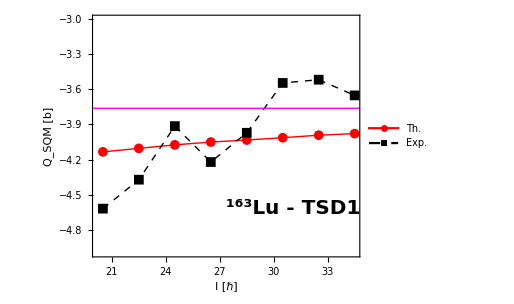

```mathematica
fig1=ListPlot[{Table[{spinsTSD1[[i]],SQMValuesKfixed[QLu163TSD1,spinsTSD1,K0][[i]]},{i,1,Length[QLu163TSD1]}],Table[{spinsTSD1[[i]],SQMValuesKfixed[QLu163TSD1Exp,spinsTSD1,K0][[i]]},{i,1,Length[QLu163TSD1Exp]}]},Frame->True,Joined->True,PlotMarkers->{Automatic, Medium},PlotRange->{Automatic,{-4.99,-3.01}},AspectRatio->0.8,FrameStyle->Directive[Black,Thick],LabelStyle->{19,Bold,Black,FontFamily->"Times"},FrameLabel->{"I [ℏ]","Q_SQM [b]"},PlotLegends->Placed[{"Th.","Exp."},{0.2,0.8}],PlotStyle->{{Red,Thick},{Black,Dashed,Thick}},Epilog->Inset[Style[Row [{Superscript["","163"],"Lu - TSD1"}],Bold,Black,FontFamily->"Arial",20],Scaled[{0.75,0.2}]],ImageSize->380];
Show[fig1,Graphics[{Magenta,Line[{{0,m1},{40,m1}}]}]]
Export["/Users/basavyr/Documents/Work/DFT/Projects/mathematica-useful-algorithms/Physics/Quadrupole-Moments/Q_SQM_163Lu.pdf",Show[fig1,Graphics[{Magenta,Line[{{0,m1},{40,m1}}]}]],ImageResolution->800];
```

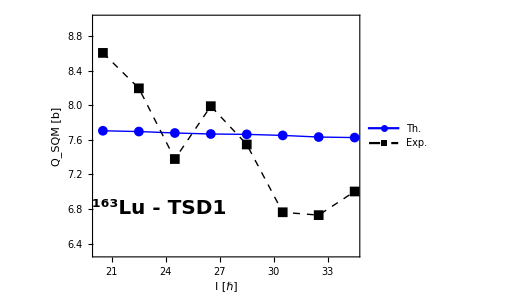

```mathematica
fig2=ListPlot[{Table[{spinsTSD1[[i]],SQMValues[QLu163TSD1,spinsTSD1][[i]]},{i,1,Length[QLu163TSD1]}],Table[{spinsTSD1[[i]],SQMValues[QLu163TSD1Exp,spinsTSD1][[i]]},{i,1,Length[QLu163TSD1Exp]}]},Frame->True,Joined->True,PlotMarkers->{Automatic, Medium},PlotRange->{Automatic,{6.3,8.99}},AspectRatio->0.8,FrameStyle->Directive[Black,Thick],LabelStyle->{19,Bold,Black,FontFamily->"Times"},FrameLabel->{"I [ℏ]","Q_SQM [b]"},PlotLegends->Placed[{"Th.","Exp."},{0.8,0.8}],PlotStyle->{{Blue,Thick},{Black,Dashed,Thick}},Epilog->Inset[Style[Row [{Superscript["","163"],"Lu - TSD1"}],Bold,Black,FontFamily->"Arial",20],Scaled[{0.25,0.2}]],ImageSize->380];
Show[fig2]
Export["/Users/basavyr/Documents/Work/DFT/Projects/mathematica-useful-algorithms/Physics/Quadrupole-Moments/Q_SQM_163Lu-2.pdf",Show[fig2],ImageResolution->800];
```

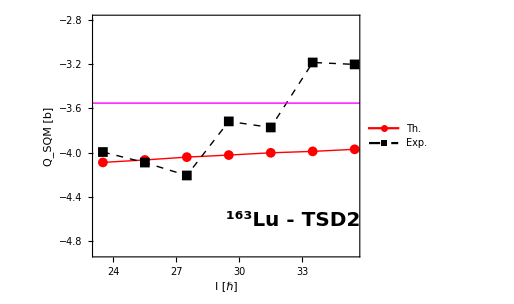

```mathematica
fig3=ListPlot[{Table[{spinsTSD2[[i]],SQMValuesKfixed[QLu163TSD2,spinsTSD2,K0][[i]]},{i,1,Length[QLu163TSD2]}],Table[{spinsTSD2[[i]],SQMValuesKfixed[QLu163TSD2Exp,spinsTSD2,K0][[i]]},{i,1,Length[QLu163TSD2Exp]}]},Frame->True,Joined->True,PlotMarkers->{Automatic, Medium},PlotRange->{Automatic,{-4.9,-2.8}},AspectRatio->0.8,FrameStyle->Directive[Black,Thick],LabelStyle->{19,Bold,Black,FontFamily->"Times"},FrameLabel->{"I [ℏ]","Q_SQM [b]"},PlotLegends->Placed[{"Th.","Exp."},{0.25,0.75}],PlotStyle->{{Red,Thick},{Black,Dashed,Thick}},Epilog->Inset[Style[Row [{Superscript["","163"],"Lu - TSD2"}],Bold,Black,FontFamily->"Arial",20],Scaled[{0.75,0.15}]],ImageSize->380];
Show[fig3,Graphics[{Magenta,Line[{{0,m2},{40,m2}}]}]]
Export["/Users/basavyr/Documents/Work/DFT/Projects/mathematica-useful-algorithms/Physics/Quadrupole-Moments/Q_SQM_163Lu-3.pdf",Show[fig3,Graphics[{Magenta,Line[{{0,m2},{40,m2}}]}]],ImageResolution->800];
```

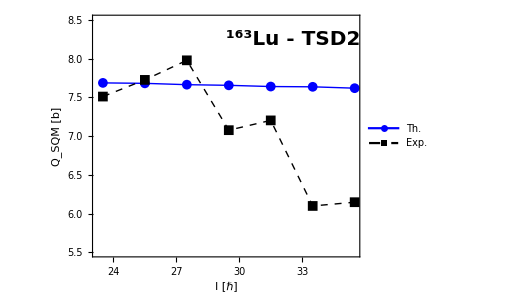

```mathematica
fig4=ListPlot[{Table[{spinsTSD2[[i]],SQMValues[QLu163TSD2,spinsTSD2][[i]]},{i,1,Length[QLu163TSD2]}],Table[{spinsTSD2[[i]],SQMValues[QLu163TSD2Exp,spinsTSD2][[i]]},{i,1,Length[QLu163TSD2Exp]}]},Frame->True,Joined->True,PlotMarkers->{Automatic, Medium},PlotRange->{Automatic,{5.5,8.5}},AspectRatio->0.8,FrameStyle->Directive[Black,Thick],LabelStyle->{19,Bold,Black,FontFamily->"Times"},FrameLabel->{"I [ℏ]","Q_SQM [b]"},PlotLegends->Placed[{"Th.","Exp."},{0.25,0.25}],PlotStyle->{{Blue,Thick},{Black,Dashed,Thick}},Epilog->Inset[Style[Row [{Superscript["","163"],"Lu - TSD2"}],Bold,Black,FontFamily->"Arial",20],Scaled[{0.75,0.9}]],ImageSize->380];
Show[fig4]
Export["/Users/basavyr/Documents/Work/DFT/Projects/mathematica-useful-algorithms/Physics/Quadrupole-Moments/Q_SQM_163Lu-4.pdf",Show[fig4],ImageResolution->800];
```